```mathematica
V[r_]=-1/r-(1.0415223038416566 ⅇ^(-0.9990999998788636 r))/r;α=2.;u0=1.*10^-8;r1=1500.;r2=u0;
```

```mathematica
sol=ParametricNDSolve[{u''[r]+(α(e-V[r])-0/r^2)u[r]==0,u[r1]==u0,u'[r1]==(*√(α(V[r1]-e)) u0*)-u0},
u,{r,r1,r2},e,Method->"Chasing",MaxSteps->Infinity,WorkingPrecision->20,MaxStepFraction->10^-3]
```

{u→ParametricFunction[<>]}

```mathematica
FindRoot[u[e][r2]==0/.sol,{e,-.0012,-.0013}]
```

{e→-0.0012937}

```mathematica
energy={};
```

```mathematica
AppendTo[energy,-e/.%]
```

{1.33732,0.186434,0.0710575,0.0374072,0.023051,0.0156184,0.00535929,0.0012937}

```mathematica
energy
```

{1.33732,0.186434,0.0710575,0.0374072,0.023051,0.0156184,0.00535929,0.0012937}

```mathematica
ene={};
ene=Flatten[Reap[Do[Sow[{i,energy[[i]]}],{i,1,6}];Sow[{10,energy[[7]]}];Sow[{20,energy[[8]]}]][[2]],1]
```

{{1,1.33732},{2,0.186434},{3,0.0710575},{4,0.0374072},{5,0.023051},{6,0.0156184},{10,0.00535929},{20,0.0012937}}

```mathematica
Solve[-1/(2 n^2)+c/(√π n^3)==-energy[[8]]/.n->20,c]
```

{{c→-0.619584}}

```mathematica
ϵ=Flatten[-Table[-1/(2 n^2)+c/(√π n^3)/.%50,{n,20}][[#]]&/@{1,2,3,4,5,6,10,20}](*the energy of perturbation*)
```

{0.849563,0.168695,0.0685023,0.0367119,0.0227965,0.0155072,0.00534956,0.0012937}

```mathematica
δϵ =Table[Abs[(ϵ[[i]]-energy[[i]])/energy[[i]]],{i,8}]
```

{0.364728,0.0951468,0.0359588,0.018586,0.0110394,0.00711693,0.00181554,0.}

```mathematica
Lδϵ={energy[[#]],δϵ[[#]]}&/@{1,2,3,4,5,6,7,8}
```

{{1.33732,0.364728},{0.186434,0.0951468},{0.0710575,0.0359588},{0.0374072,0.018586},{0.023051,0.0110394},{0.0156184,0.00711693},{0.00535929,0.00181554},{0.0012937,0.}}

```mathematica
LδE=Join[(*Partition[N[1/(2#^2)]&/@{1,2,3,4,5,6,10,20},1]*)Partition[energy,1],Partition[δE,1],2]
```

{{1.33732,0.626118},{0.186434,0.329521},{0.0710575,0.21816},{0.0374072,0.164599},{0.023051,0.132358},{0.0156184,0.110735},{0.00535929,0.0670411},{0.0012937,0.0337756}}

```mathematica
δE=Join[Table[Abs[(1/(2 i^2)-energy[[i]])/energy[[i]]],{i,6}],{Abs[(1/(2 10^2)-energy[[7]])/energy[[7]]]},{Abs[(1/(2 20^2)-energy[[8]])/energy[[8]]]}]
```

{0.626118,0.329521,0.21816,0.164599,0.132358,0.110735,0.0670411,0.0337756}

```mathematica
LδE
Lδϵ
```

{{0.5,0.626118},{0.125,0.329521},{0.0555556,0.21816},{0.03125,0.164599},{0.02,0.132358},{0.0138889,0.110735},{0.005,0.0670411},{0.00125,0.0337756}}

{{1.33732,0.364728},{0.186434,0.0951468},{0.0710575,0.0359588},{0.0374072,0.018586},{0.023051,0.0110394},{0.0156184,0.00711693},{0.00535929,0.00181554},{0.0012937,0.}}

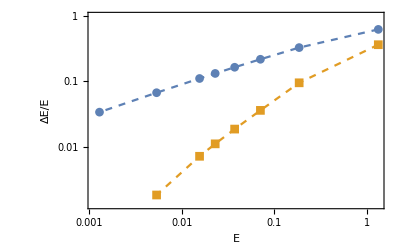

```mathematica
ListLogLogPlot[{LδE,Lδϵ},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->Reverse[{"ΔE/E","E"}],RotateLabel->False,ImageSize->Full,PlotStyle->Dashed]
```

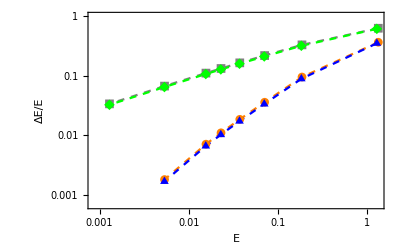

```mathematica
ListLogLogPlot[{Lδϵ,LδE,LδLepage,LδLepageϵ},Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->Full,FrameLabel->{"E","ΔE/E"},RotateLabel->False(*,PlotStyle->Dashed*),AxesOrigin->{0.001,0.001},PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}}]
```

```mathematica
Lepageenergy={1.28711542,0.183325753,0.0703755485,0.0371495726,0.0229268241,0.0155492598,0.00534541931,0.00129205010}
```

{1.28712,0.183326,0.0703755,0.0371496,0.0229268,0.0155493,0.00534542,0.00129205}

```mathematica
δLepage=Join[Table[Abs[(1/(2 i^2)-Lepageenergy[[i]])/Lepageenergy[[i]]],{i,6}],{Abs[(1/(2 10^2)-Lepageenergy[[7]])/Lepageenergy[[7]]]},{Abs[(1/(2 20^2)-Lepageenergy[[8]])/Lepageenergy[[8]]]}]
```

{0.611534,0.318154,0.210584,0.158806,0.127659,0.106781,0.0646197,0.0325453}

```mathematica
LδLepage=Join[Partition[(*N[1/(2#^2)]&/@{1,2,3,4,5,6,10,20}*)Lepageenergy,1],Partition[δLepage,1],2]
```

{{1.28712,0.611534},{0.183326,0.318154},{0.0703755,0.210584},{0.0371496,0.158806},{0.0229268,0.127659},{0.0155493,0.106781},{0.00534542,0.0646197},{0.00129205,0.0325453}}

```mathematica
Solve[-1/(2 n^2)+c/(√π n^3)==-Lepageenergy[[8]]/.n->20,c]
```

{{c→-0.596255}}

```mathematica
Lepageϵ=Flatten[-Table[-1/(2 n^2)+c/(√π n^3)/.%171,{n,20}][[#]]&/@{1,2,3,4,5,6,10,20}]
δLepageϵ =Table[Abs[(Lepageϵ[[i]]-Lepageenergy[[i]])/Lepageenergy[[i]]],{i,8}]
```

{0.836401,0.16705,0.0680148,0.0365063,0.0226912,0.0154463,0.0053364,0.00129205}

{0.350174,0.08878,0.0335444,0.0173168,0.0102769,0.00662152,0.00168715,0.}

```mathematica
LδLepageϵ={Lepageenergy[[#]],δLepageϵ[[#]]}&/@{1,2,3,4,5,6,7,8}
```

{{1.28712,0.350174},{0.183326,0.08878},{0.0703755,0.0335444},{0.0371496,0.0173168},{0.0229268,0.0102769},{0.0155493,0.00662152},{0.00534542,0.00168715},{0.00129205,0.}}

```mathematica
FindFit[ene,-(-1/(2 n^2)+c/(√π n^3)),c,n]
```

{c→-1.47344}

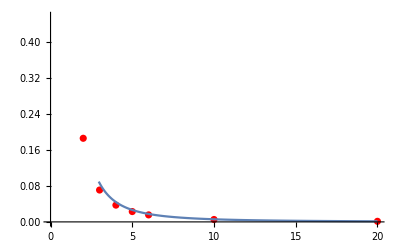

```mathematica
Show[ListPlot[ene,PlotStyle->Red],Plot[-(-1/(2 n^2)+c/(√π n^3))/.{c->-1.4734380450094016},{n,1,20}]]
```